## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /home/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.212641 GB

seed file: /home/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: dtopa-latitude-5491,  MM v. 12.0.0 for Linux x86

date: Mar 11, 2020, time: 16:44:60

nb: /home/dantopa/Mathematica_files/nb/ert/rcs/fourier/frequency-decomposition-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.212641 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
fticks={{Automatic,Automatic},{{{1,-π},{91,-π/2},{181,0},{271,π/2},{361,π}},Automatic}};
nticks={{Automatic,Automatic},{π/2 ints,Automatic}};
```

```mathematica
𝕔=299792458;
```

#### functions

```mathematica
Clear[sty];
sty[s_String]:=Style[s,FontFamily->"TimesNewRoman"]
```

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## grab a frequency

```mathematica
ν=meanRCSᵀ[[3]];
m=Length[ν]
μ=Mean[ν]
```

28

21.579

```mathematica
ListPlot[ν,
Joined->True,
Frame->True];
```

ListPlot::lpn: ν is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## resolve

### mesh

```mathematica
x=Range[0,m-1]/(m-1)
```

{0,1/27,2/27,1/9,4/27,5/27,2/9,7/27,8/27,1/3,10/27,11/27,4/9,13/27,14/27,5/9,16/27,17/27,2/3,19/27,20/27,7/9,22/27,23/27,8/9,25/27,26/27,1}

### system matrix

```mathematica
one=x-x+1;
A={one,x,x^2,x^3,x^4}ᵀ;
b=ν;
```

```mathematica
Dimensions[A]
Dimensions[b]
```

{28,5}

{28}

```mathematica
A//mf
```

(1 | 0 | 0 | 0 | 0
1 | 1/27 | 1/729 | 1/19683 | 1/531441
1 | 2/27 | 4/729 | 8/19683 | 16/531441
1 | 1/9 | 1/81 | 1/729 | 1/6561
1 | 4/27 | 16/729 | 64/19683 | 256/531441
1 | 5/27 | 25/729 | 125/19683 | 625/531441
1 | 2/9 | 4/81 | 8/729 | 16/6561
1 | 7/27 | 49/729 | 343/19683 | 2401/531441
1 | 8/27 | 64/729 | 512/19683 | 4096/531441
1 | 1/3 | 1/9 | 1/27 | 1/81
1 | 10/27 | 100/729 | 1000/19683 | 10000/531441
1 | 11/27 | 121/729 | 1331/19683 | 14641/531441
1 | 4/9 | 16/81 | 64/729 | 256/6561
1 | 13/27 | 169/729 | 2197/19683 | 28561/531441
1 | 14/27 | 196/729 | 2744/19683 | 38416/531441
1 | 5/9 | 25/81 | 125/729 | 625/6561
1 | 16/27 | 256/729 | 4096/19683 | 65536/531441
1 | 17/27 | 289/729 | 4913/19683 | 83521/531441
1 | 2/3 | 4/9 | 8/27 | 16/81
1 | 19/27 | 361/729 | 6859/19683 | 130321/531441
1 | 20/27 | 400/729 | 8000/19683 | 160000/531441
1 | 7/9 | 49/81 | 343/729 | 2401/6561
1 | 22/27 | 484/729 | 10648/19683 | 234256/531441
1 | 23/27 | 529/729 | 12167/19683 | 279841/531441
1 | 8/9 | 64/81 | 512/729 | 4096/6561
1 | 25/27 | 625/729 | 15625/19683 | 390625/531441
1 | 26/27 | 676/729 | 17576/19683 | 456976/531441
1 | 1 | 1 | 1 | 1)

```mathematica
c=LeastSquares[A,b]
```

{33.4222,-109.349,243.419,-173.331,24.2802}

```mathematica
f[z_]=c.{1,z,z^2,z^3,z^4}
```

33.4222-109.349 z+243.419 z^2-173.331 z^3+24.2802 z^4

```mathematica
ζ={x,ν}ᵀ;
```

```mathematica
g000=ListPlot[ζ,PlotStyle->Black];
```

```mathematica
g001=Plot[f[z],{z,-0.15,1},PlotPoints->50];
g003=Show[{g000,g001},Frame->True];
```

```mathematica
glines=Graphics[{Red,Table[
Line[{{x[[k]],ν[[k]]},{x[[k]],f[x[[k]]]}}]
,{k,m}]}];
```

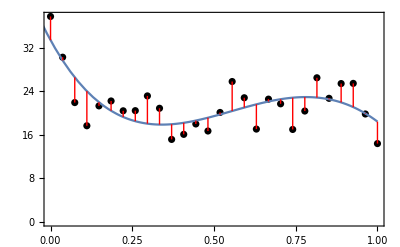

```mathematica
g004=Show[{g003,glines}]
```

```mathematica
r=ν-f[x];
(r.r)/m
```

10.6995

```mathematica
LegendreP[5,z]
CoefficientList[%,z]
```

1/8 (15 z-70 z^3+63 z^5)

{0,15/8,0,-35/4,0,63/8}

```mathematica
ω=4;
T=Table[
amplitudes=CoefficientList[LegendreP[k,z],z];
PadRight[amplitudes,ω+1]
,{k,0,ω}]ᵀ;
T//mf
```

(1 | 0 | -1/2 | 0 | 3/8
0 | 1 | 0 | -3/2 | 0
0 | 0 | 3/2 | 0 | -15/4
0 | 0 | 0 | 5/2 | 0
0 | 0 | 0 | 0 | 35/8)

```mathematica
𝕓=Inverse[T].c
```

{119.418,-213.348,176.153,-69.3325,5.54975}

```mathematica
g[z_]=Simplify[
𝕓.Table[
LegendreP[k,z]
,{k,0,ω}]]
```

33.4222-109.349 z+243.419 z^2-173.331 z^3+24.2802 z^4

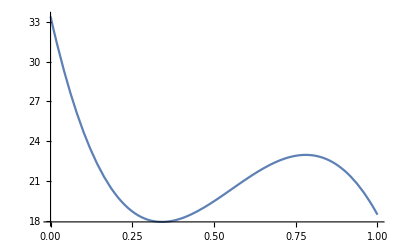

```mathematica
Plot[g[z],{z,0,1}]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```